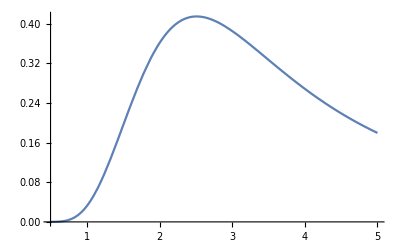

```mathematica
Clear["Global`*"]
Clear[Subscript]
Z=Exp[8/T]+4Exp[0/T]+4Exp[0/T]+2Exp[-8/T]+4Exp[0/T]+Exp[8/T];
A=-T Log[Z];
Cvmol=-T D[A,{T,2}]/4;
Plot[Cvmol,{T,0.5,5}]
```

```mathematica
Table[Cvmol, {T,0.5,5,0.05}]
```

{0.0000432135,0.000152944,0.000431885,0.00102626,0.00213136,0.00397704,0.00680649,0.0108531,0.0163197,0.0233628,0.0320823,0.0425176,0.0546476,0.0683947,0.083632,0.100191,0.117872,0.13645,0.15569,0.175346,0.195179,0.214956,0.234457,0.253481,0.271847,0.289397,0.305999,0.321544,0.335946,0.349143,0.361096,0.371784,0.381203,0.389368,0.396304,0.402048,0.406649,0.410159,0.412638,0.414149,0.414759,0.414533,0.413539,0.411844,0.40951,0.406602,0.403179,0.399297,0.395012,0.390372,0.385426,0.380218,0.374787,0.369172,0.363406,0.357521,0.351544,0.345502,0.339417,0.33331,0.3272,0.321103,0.315033,0.309003,0.303024,0.297107,0.291259,0.285488,0.2798,0.2742,0.268693,0.263281,0.257967,0.252755,0.247644,0.242637,0.237733,0.232934,0.228239,0.223647,0.219159,0.214772,0.210486,0.2063,0.202212,0.198221,0.194325,0.190522,0.18681,0.183189,0.179655}